Seminarska naloga

Avtor: Matjaž Levstek
Računalniška orodja v matematiki

## LINEARNA FUNKCIJA

Linearna funkcija je funkcija, ki jo lahko zapišemo z enačbo oblike:
f (x) = kx + n,
 kjer sta koeficienta k in n poljubni realni števili(k ni 0 ).

## GRAF LINEARNE FUNKCIJE

```mathematica
SetOptions[EvaluationNotebook[],Background->LightBrown]
```

Graf linearne funkcije je premica:

```mathematica
f[x] = 2x +1
```

1+2 x

```mathematica
Plot[f[x],{x, -3,3}]
```

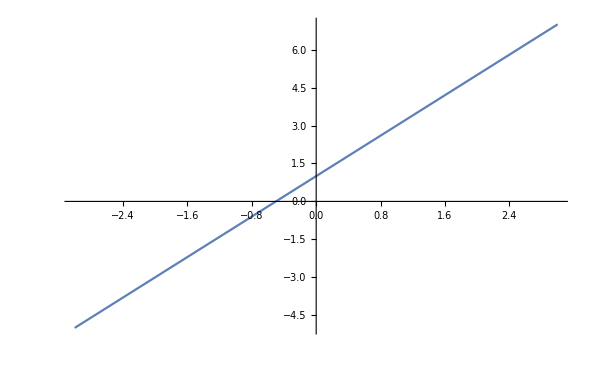

Število N pomeni presečišče grafa z ordinatno osjo. Imenujemo ga začetna vrednost ali odsek na osi y. Število K pa določa smer in strmino premice. Imenujemo ga smerni koeficient premice.  Točko ki jo določa k dobimo tako, da se iz točke N pomaknemo za eno enoto v desno in za K enot navzgor (oziroma navzdol, če je k negativen).
Ker dve točki določata premico, lahko graf narišemo tako, da izračunamo koordinate dveh točk ali pa si pomagamo kar s točkama, ki ju določata k in n. 
Koeficient lahko izračunamo tako, da izberemo dve točki na premici in spremembo koordinat y  in spremembo x delimo.

```mathematica
g[x]= 1x +1
```

1+x

```mathematica
h[x]= 1
```

1

```mathematica
e[x] = -1x +1
```

1-x

```mathematica
Plot[{g[x],h[x], e[x]},{x, -1.5, 1.5}, PlotLabels->"Expressions"]
```

```mathematica
Če je k > 0: fukcija narašča,
Če je k = 0: funkcija je konstantna (Graf je vzporeden abscisni osi.),
Če je k < 0: funkcija pada
```

```mathematica
OBLIKE LINEARNE FUNKCIJE
```

Eksplicitna oblika enačbe premice uporabimo, ko enačbo premice zapišemo kot enačbo grafa linearne funkcije: y = kx + n.
Tak zapis je jasen, saj se da lepo prebrati, kje premica seka ordinato in kolikšen je naklon premice.

Implicitna oblika enačbe premice nam omogoči zapis vseh premic v ravnini. Ta vrsta enačbe nam žal nič ne pomaga pri risanju grafov. Njena oblika je ax + by + c = 0

Za lažje risanje uporabljamo odsekovno(segmentno) obliko enačbe premice: x/m + y/n = 1
Števili m in n pomenita odseka, ki ju premica omejuje na absicsni(m) in ordinatni osi(n).

```mathematica
ODNOSI MED PREMICAMI V PROSTORU
```

Dve premici lahko ležita v različnih medsebojnih legah:

1. Premici sta vzporedni, če nimata nobene skupne točke. Taki premici imata enak smerni koeficient(k1= k)-pogoj vzporednosti.

```mathematica
Plot[{3x+ 1, 3x -3},{x,-1.5, 1.5}]
```

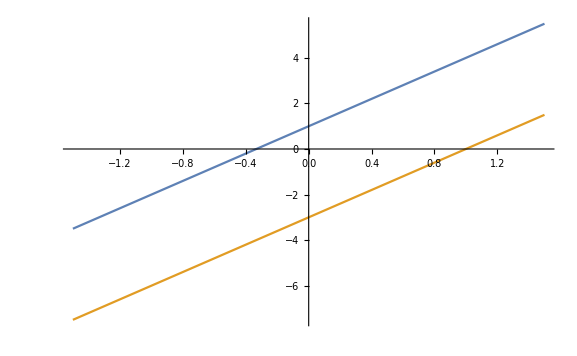

```mathematica
2. Premici, ki se sekata, imata natanko eno skupno točko, ki jo imenujemo presečišče.
```

```mathematica
Plot[{x+2, -2x }, {x, -1, 1}]
```

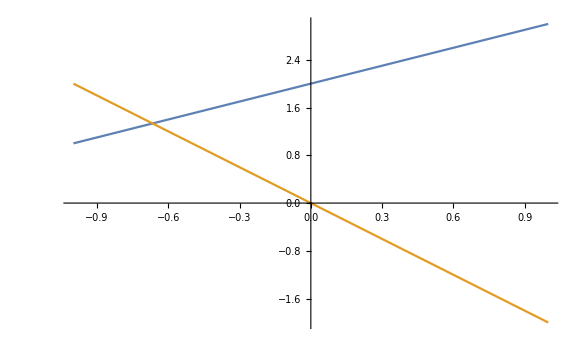

```mathematica
3. Premici, ki se sekata pod pravim kotom sta pravokotni. Smerni koeficient prve premice mora biti obratna in nasprotna vrednost smernega koeficienta druge premice
(k1 = - (1/ k) )-pogoj pravokotnosti.
```

```mathematica
Plot[{x, -x},{x, -2,2}]
```

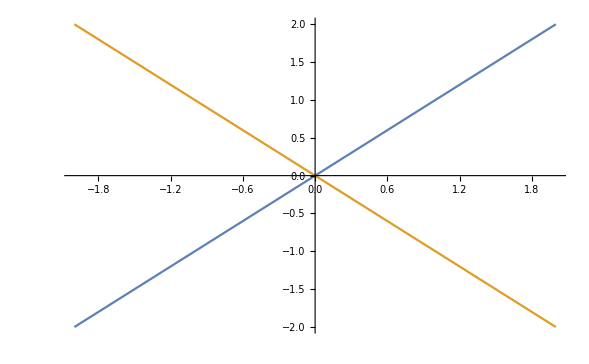

KOT MED PREMICAMA

```mathematica
Kot, ki ga oklepata premica in abscisna os je naklonski kot. Za naklonski kot premice s smernim koeficientom k velja formula:
tg α = k
```

Kot med premicama izračunamo s pomočjo naklonskih kotov dveh premic (φ = |α2 − α1| ), ali pa s pomočjo smernih koeficientov:
tg  φ = |(k1-k)/(1+k1k)|

```mathematica
Plot[{x, -x},{x, -2,2}]
```

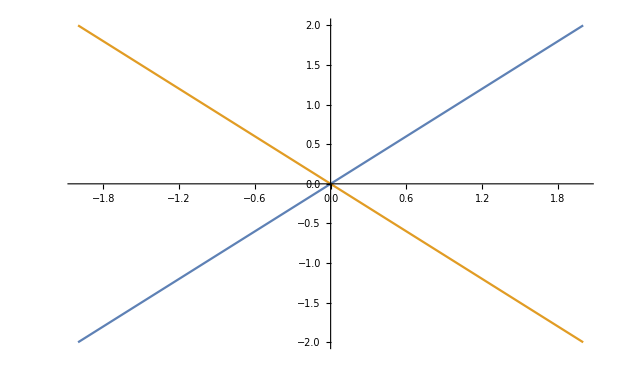

SIMETRALI

Premico, katere enačba je , y = x  imenujemo simetrala lihih kvadrantov (razpolavlja I. in III. kvadrant – na sliki spodaj modra premica). Premico, katere enačba je y = -x , imenujemo simetrala sodih kvadrantov (razpolavlja II. in IV. kvadrant – na sliki spodaj oranžna premica).

```mathematica
Plot[{x, -x},{x,-1,1}]
```

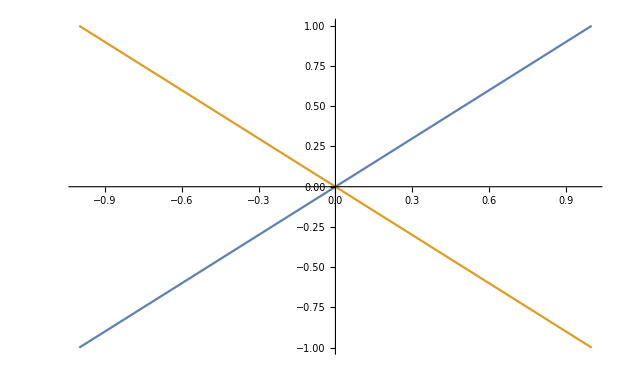

## SISTEM LINEARNIH ENAČB

Pri iskanju presečišča dveh premic enačimo predpisa:
k1x +n1 = kx + n
Rezultat, ki ga dobimo je abcisa presečišča premic. S pomočjo enega izmed predpisov premic nato izračunamo ordinato presečišča. 
Zgled:

```mathematica
f[x]
```

1+2 x

```mathematica
k[x]= 4x - 2
```

-2+4 x

```mathematica
Solve[f[x]==k[x]]
```

{{x→3/2}}

```mathematica
y = 1+3/2*2
```

4

```mathematica
Presečišče je v točki T (3/2, 4)
```

```mathematica
Plot[{f[x],k[x]},{x,-2,2}]
```

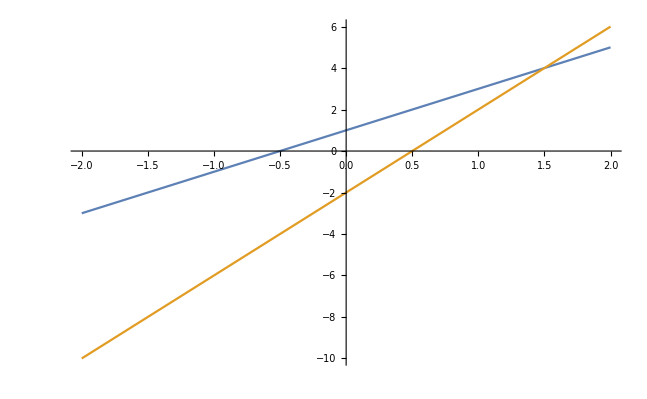

```mathematica
ClearAll[x,y]
```

In pa to:

```mathematica
Solve[{3x + 2y -2 == 0, 7x + 5y+4==0},{x, y}]
```

{{x→18,y→-26}}

```mathematica
Presečišče je v točki T (18, 26)
```

```mathematica
Plot[{-3x/2+1,-7x/5-4/5 },{x, -20,20}]
```